## (*Gumble vs Normal distribution*)

```mathematica
(*PDF[OrderDistribution[{NormalDistribution[μ,σ],n},n],z]*)
```

```mathematica
PDF[NormalDistribution[μ,σ]]
```

Function[x,(ⅇ^(-1/2 (-0.5+x)^2))/(√(2 π))]

```mathematica
μ=0;σ=1;
x1=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{10000,10000}];
```

```mathematica
(*1000 samples in each 100'000 random numbers from a Normal distribution*)
```

```mathematica
μ=0.5;σ=1;
x2=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{10000,10000}];
```

```mathematica
μ=0;σ=2;
x3=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{10000,10000}];
```

```mathematica
μ=3;σ=4; (**)
x4=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{10000,10000}];
```

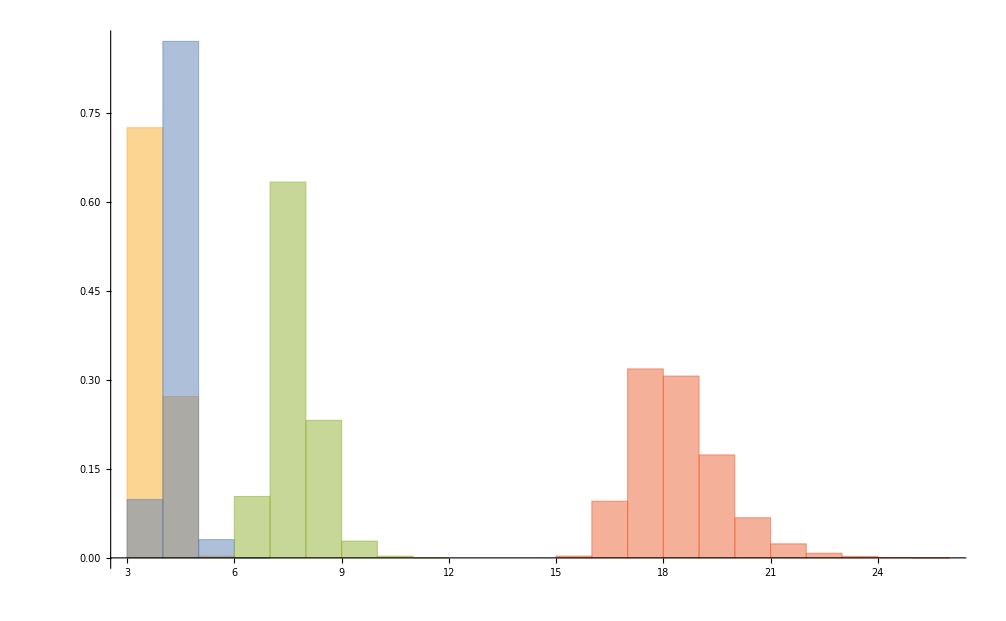

```mathematica
Histogram[{x1,x2,x3,x4},Automatic,"PDF"]
```

## For a size similar to our simulation:

```mathematica
x=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{10,512^3}]; (*Assume we run 5 simulations but we have 512^3 points*)
```

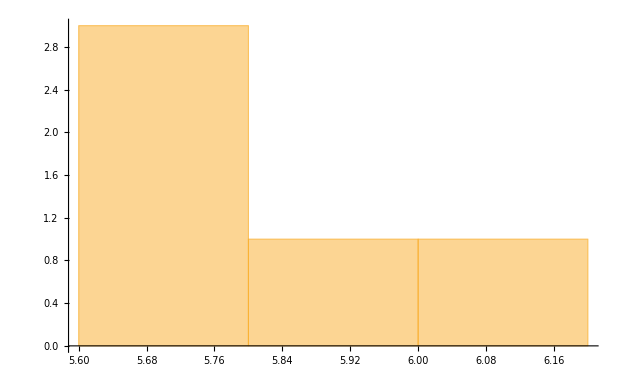

```mathematica
Histogram[{x},Automatic,"PDF"]
```

```mathematica
meanvalue=Mean[x]
```

5.79067

```mathematica
var = StandardDeviation[x]
```

0.179902

```mathematica
mu=Mean[x];sigma=StandardDeviation[x];
```

```mathematica
pdf=PDF[NormalDistribution[mu,sigma]/.FindDistributionParameters[x,NormalDistribution[mu,sigma]]];
```

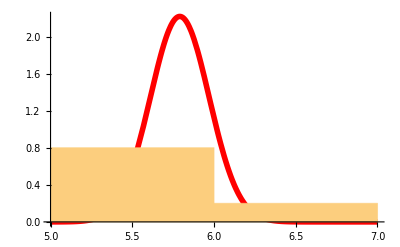

```mathematica
Show[Plot[pdf[x],{x,5,7},PlotStyle->Directive[Thickness[0.01],Red]],Histogram[x,{5,7,1},"PDF"]]
```

```mathematica
|
```

## For different sample size let’s look at the maxima distribution:

```mathematica
(*μ=0;σ=1;n=100;
x1=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{10000,n}]; *)
```

```mathematica
(*1000 samples in each 100'000 random numbers from a Normal distribution*)
```

```mathematica
(*Quit[x];*)
```

{data[1],data[2]}

```mathematica
Clear[data,x,M,n,var,avg];
```

```mathematica
number=100;M=Array[data,number];M2=Array[avg,number];M3=Array[var,number];
```

```mathematica
For[i=1,i<number,i=i+2,μ=0;σ=1;n=1000;n=i^2;
data[i]=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{5000,n}]; 
avg[i]=Mean[data[i]];var[i]=StandardDeviation[data[i]];]
```

```mathematica
avgTable=Table[{i^2,avg[i]},{i,1,number,1}];
```

```mathematica
varTable=Table[{i^2,var[i]},{i,1,number,1}];
```

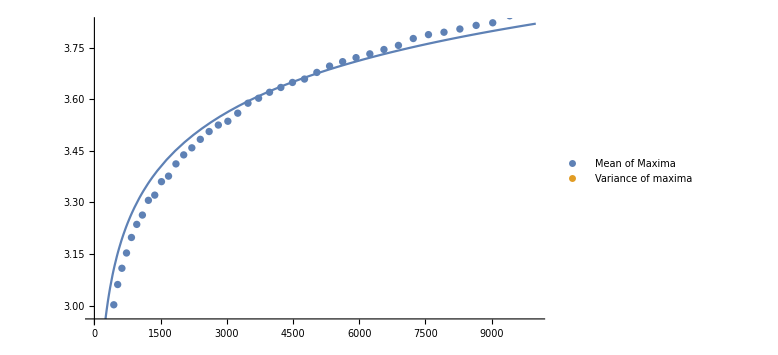

```mathematica
Show[Plot[0.89 √(2Log[ m]),{m,2,10000},ImageSize->Large],ListPlot[{avgTable,varTable}, ImageSize->Large,PlotLegends->{"Mean of Maxima","Variance of maxima"}]]
```

## Testing the relation of Gambel mean with variance of the Gaussian distribution

```mathematica
Clear[data,x,M,n,var,avg];
```

```mathematica
number=100;M=Array[data,number];M2=Array[avg,number];M3=Array[var,number];
```

```mathematica
For[i=1,i<number,i=σ+1,μ=0;σ=i;n=5000;
data[i]=Max[#]&/@RandomVariate[NormalDistribution[μ,σ],{1000,n}]; 
avg[i]=Mean[data[i]];var[i]=StandardDeviation[data[i]];]
```

```mathematica
avgTable=Table[{i,avg[i]},{i,1,number,1}];
```

```mathematica
varTable=Table[{i,var[i]},{i,1,number,1}];
```

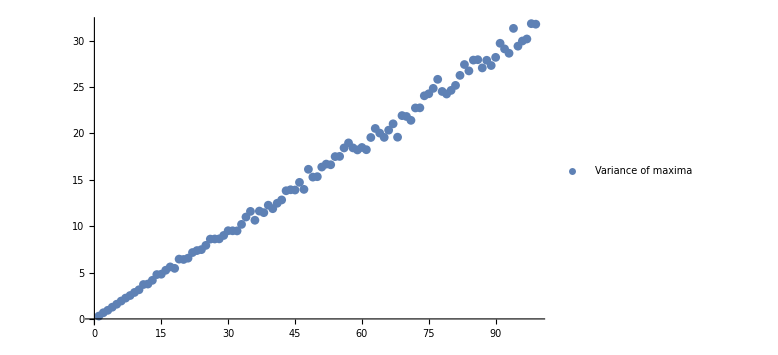

```mathematica
ListPlot[varTable, ImageSize->Large,PlotLegends->{"Variance of maxima"}]
```

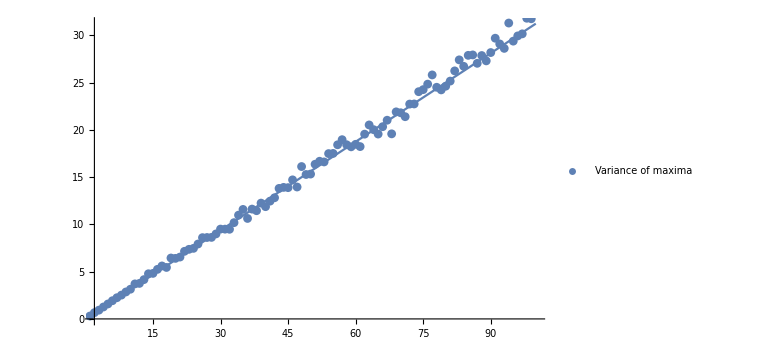

```mathematica
Show[Plot[m/3.2,{m,2,100},ImageSize->Large],
ListPlot[{varTable}, ImageSize->Large,PlotLegends->{"Variance of maxima"}]]
```

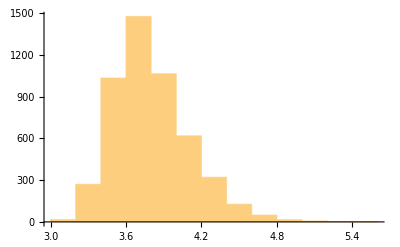

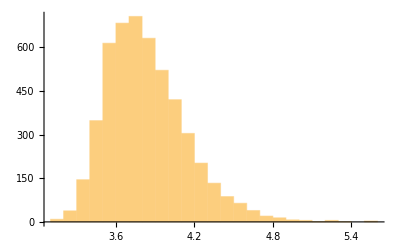

```mathematica
Do[Print[Histogram[data[i],PlotRange->{{-5,5},All},Automatic,ChartLegends->ToString[i^2]]],{i,91,100,6}]
```

## Useful commands

```mathematica
x=Max[#]&/@RandomVariate[LogNormalDistribution[3.2,0.4],{1000,100000}];
Show[Histogram[x,Automatic,"PDF"],Plot[PDF[OrderDistribution[{LogNormalDistribution[3.2,0.4],100000},100000],z],{z,110,200}]]
```

```mathematica
num=100
```

100

```mathematica
data=Max[#]&/@RandomVariate[NormalDistribution[3.2,0.4],10]
```

{2.70456,3.40419,2.35173,3.75439,3.3904,3.21385,3.56963,2.66354,2.57061,2.58829}

```mathematica
x=RandomVariate[NormalDistribution[0,1],{3,2}]
```

{{-1.06678,0.863831},{0.280517,-0.21756},{-0.565242,-0.572392}}

```mathematica
Dimensions[x]
```

{3,2}

```mathematica
#-1&/@x
```

{{-2.06678,-0.136169},{-0.719483,-1.21756},{-1.56524,-1.57239}}

```mathematica
Max[#]&/@x
```

{0.11813,1.24024,1.48201,0.982603,1.83956,0.301625,0.166921,1.04339,-0.589611,0.895182}

```mathematica
Max[#]&/@{1.0288727387635088,-0.7473639869769068,-0.6583004469030391,-0.501391890258493}
```

{1.02887,-0.747364,-0.6583,-0.501392}

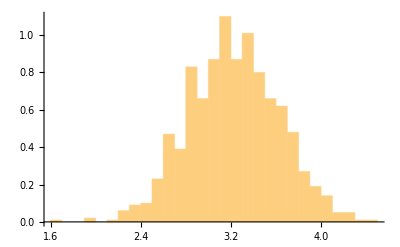

```mathematica
Show[
Histogram[data,Automatic,"ProbabilityDensity"]]
```

```mathematica
OrderDistribution[{NormalDistribution[0,1],100},1]
```

OrderDistribution[{NormalDistribution[0,1],100},1]

```mathematica
(*OrderDistributionpaclet:ref/OrderDistribution[{dist,n},k]represents thek^th-order statistics distribution fornobservations from the distributiondist.*)
```